{{wx→-1/(√65),wy→4 √(3/65)},{wx→1/(√65),wy→-4 √(3/65)}}

-1.61245

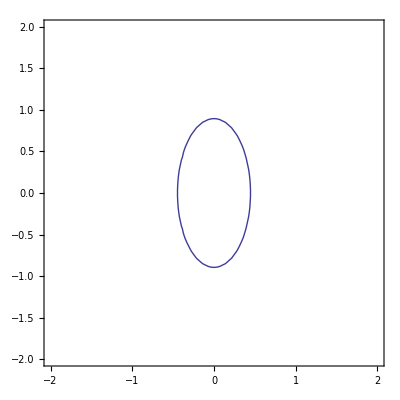

{{1,1/4},{{1,0},{0,1}}}

```mathematica
ClearAll["Global`*"]
$T = 1/10;
$D1 = {{1,0},{0, 1/4}};
MatrixForm[%];
zT1 := {x,y}.$D1.{x,y}/2;
v1 = {√3/2, 1/2};
v2 = {1/2, √3/2};
$v = v1;
$w := {wx,wy};
$sol = Solve[{$w.$D1.$w/2 == $T, $v.$D1.$w  ==0},$w]
$w = $w/.$sol[[2]];

width = N[2*{-$v[[2]], $v[[1]]}.$w]

Show[ContourPlot[{zT1==$T}, {x,-2,2}, {y, -2,2}]]

Eigensystem[$D1]
```